```mathematica
ClearAll[unblendedCosCircleSmoothie]

unblendedCosCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot
		},
		circleList=Circle[{-maxRadius-5,0},#1]&/@Abs@fourierCoeff;
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}];
		manipulatedCoord=Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}];
		maxRadius=Max[Abs@fourierCoeff];
		lineList=Line[{{-maxRadius-5,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
		styledLines=MapThread[Style,{lineList,color}];
		
		prePlot=MapThread[Times,{fourierCoeff,Cos[(Range[numCir]*(variable+$time))-(Pi/2)]}];
		plotList=Plot[#1,{variable,0,10},PlotStyle->#2]&@@@(Transpose[{prePlot,color}]);
		
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				Plot[#3,{variable,0,10},PlotStyle->#4,PlotRange->All],PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,styledLines,prePlot,color}]
	
	]
```

```mathematica
ClearAll[circleCosSmoothie2]

circleCosSmoothie2[function_,variable_Symbol,numCir_Integer]:=
	Block[{
		fourierConstant=FourierCosCoefficient[function,variable,0]//ComplexExpand,
		fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
		basicCoord,manipulatedCoord,lastYCoord,totalRadius,combinedCir,cirCenter,
		cirArguments,finalPlot,lineSeries,centerOfFirstCir,listOfCoord,lastLinetoYaxis,
		lastXCoord,plotCoord,plotAllign
	
	
	},
	
	totalRadius=Total[Abs@fourierCoeff];
	basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*$time]}];
	manipulatedCoord=Join[
		Take[
			Transpose[
			{(basicCoord-totalRadius-5)/.Cos->Sin,basicCoord}],1],
		Drop[Transpose[{basicCoord/.Cos->Sin,basicCoord}],1]];
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-totalRadius-5,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=Total[MapThread[Times,{fourierCoeff,Cos[((Range[numCir])*(variable+$time))]}]];
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= Line[#1]&@(Append[manipulatedCoord,lastLinetoYaxis]);

	Animate[
			Show[
				Graphics[{Sequence@@#1,#2},Axes->True],
				Plot[#3,{variable,0,3*#4},PlotRange->Full],
				PlotRange->{{-3*#4,3#4},{-#4,#4}}
								],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord,totalRadius}]
	
	
	]
```

```mathematica
ClearAll[unblendedSinCircleSmoothie]

unblendedSinCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierSinCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot
		},
		circleList=Circle[{-maxRadius-5,0},#1]&/@Abs@fourierCoeff;
		basicCoord=MapThread[Times,{fourierCoeff,Sin[Range[numCir]*variable]}];
		manipulatedCoord=Transpose[{basicCoord-maxRadius-5,basicCoord/.Sin->Cos}];
		maxRadius=Max[Abs@fourierCoeff];
		lineList=Line[{{-maxRadius-5,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
		styledLines=MapThread[Style,{lineList,color}];
		
		prePlot=MapThread[Times,{fourierCoeff,Sin[(Range[numCir]*(variable+$time))+(Pi/2)]}];
		plotList=Plot[#1,{variable,0,10},PlotStyle->#2]&@@@(Transpose[{prePlot,color}]);
		
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				Plot[#3,{variable,0,10},PlotStyle->#4,PlotRange->All],PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,styledLines,prePlot,color}]
	
	]
```

```mathematica
ClearAll[circleSinSmoothie2]

circleSinSmoothie2[function_,variable_Symbol,numCir_Integer]:=
	Block[{
		fourierConstant=FourierSinCoefficient[function,variable,0]//ComplexExpand,
		fourierCoeff=Table[FourierSinCoefficient[function,variable,p],{p,1,numCir}],
		basicCoord,manipulatedCoord,lastYCoord,totalRadius,combinedCir,cirCenter,
		cirArguments,finalPlot,lineSeries,centerOfFirstCir,listOfCoord,lastLinetoYaxis,
		lastXCoord,plotCoord,range
	
	},
	
	totalRadius=Total[Abs@fourierCoeff];
	basicCoord=MapThread[Times,{fourierCoeff,Sin[Range[numCir]*$time]}];
	manipulatedCoord=Join[
		Take[
			Transpose[
			{(basicCoord-totalRadius-5)/.Sin->Cos,basicCoord}],1],
		Drop[Transpose[{basicCoord/.Sin->Cos,basicCoord}],1]];
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-totalRadius-5,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=Total[MapThread[Times,{fourierCoeff,Sin[((Range[numCir])*(variable+$time))]}]];
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= Line[#1]&@(Append[manipulatedCoord,lastLinetoYaxis]);
	
	range=(2Pi)*totalRadius;

	Animate[
			Show[
				Graphics[{Sequence@@#1,#2},Axes->True],
				Plot[#3,{variable,0,3*#4},PlotRange->Full],
				PlotRange->{{-3*#4,3#4},{-#4,#4}}
								],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord,totalRadius}]
	
	
	]
```

```mathematica
ClearAll[fourierCircleCookBook]
fourierCircleCookBook[function_,variable_Symbol,numCir_Integer]:=
Which[
	PossibleZeroQ[function-(function/.variable->(-variable))],
		Row[
			{unblendedCosCircleSmoothie[function,variable,numCir],
			circleCosSmoothie2[function,variable,numCir],
			Plot[function,{variable,-30,30},PlotStyle->Black,Frame->True,ImageSize->Medium,Axes->False]}
			],
	PossibleZeroQ[function+(function/.variable->(-variable))],
		Row[
			{unblendedSinCircleSmoothie[function,variable,numCir],
			circleSinSmoothie2[function,variable,numCir],
			Plot[function,{variable,-30,30},PlotStyle->Black,Frame->True,ImageSize->Medium,Axes->False]}
			],
	True,
	circleSmoothietheRest[function,variable,numCir]
	]
```

```mathematica
?ImageSize
```

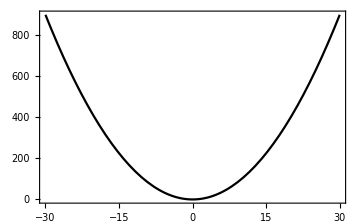

```mathematica
fourierCircleCookBook[x^2,x,10]
```

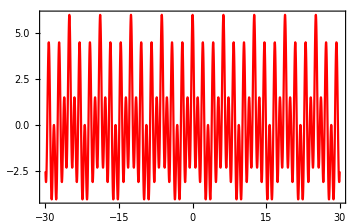

```mathematica
fourierCircleCookBook[Cos[x]+2Cos[3x]+3Cos[6x],x,10]
```

```mathematica
fourierCircleCookBook[Sin[3x]+5Sin[2x],x,10]
```

```mathematica
fourierCircleCookBook[Sin[3x]+5Sin[2x]+Cos[x],x,10]
```

Cos[x]+5 Sin[2 x]+Sin[3 x]

Drop::drop: Cannot drop positions -10 through -1 in {5 Sin[2 x],Sin[3 x]}.

Drop::drop: Cannot drop positions 1 through 10 in {5 Sin[2 x],Sin[3 x]}.

Drop::drop: Cannot drop positions -10 through -1 in {{5,{Sin[2],Sin[x]}},{Sin[3],Sin[x]}}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 4 in Drop[{{5,{Sin[2],Sin[x]}},{Sin[3],Sin[x]}},1,-10,{{5,{Sin[2],Sin[x]}},{Sin[3],Sin[x]}},10].

MapThread::mptd: Object Drop[{{5,{Sin[2],Sin[x]}},{Sin[3],Sin[x]}},1,-10] at position {2, 1} in MapThread[Times,{Drop[{{5,{Sin[2],Sin[x]}},{Sin[3],Sin[x]}},1,-10],{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],Cos[5 $time],Cos[6 $time],Cos[7 $time],Cos[8 $time],Cos[9 $time],Cos[10 $time]}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object Drop[{{5,{Sin[2],Sin[x]}},{Sin[3],Sin[x]}},1,-10] at position {2, 1} in MapThread[Times,{Drop[{{5,{Sin[2],Sin[x]}},{Sin[3],Sin[x]}},1,-10],{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],Sin[5 $time],Sin[6 $time],Sin[7 $time],Sin[8 $time],Sin[9 $time],Sin[10 $time]}}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {-5+MapThread[Times,{Drop[{{5,{«2»}},{Sin[«1»],Sin[«1»]}},1,-10],{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],Sin[5 $time],Sin[6 $time],Sin[7 $time],Sin[8 $time],Sin[9 $time],Sin[10 $time]}}]-Total[Abs[Drop[{{«2»},{«2»}},10]]]-Total[Abs[Drop[{{«2»},{«2»}},1,-10]]],MapThread[Times,{Drop[{{5,{Sin[«1»],Sin[«1»]}},{Sin[3],Sin[x]}},1,-10],{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],«3»,Cos[8 $time],Cos[9 $time],Cos[10 $time]}}]} cannot be transposed.

Transpose::nmtx: The first two levels of {MapThread[Times,{Drop[{{5,{Sin[«1»],Sin[«1»]}},{Sin[3],Sin[x]}},1,-10],{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],Sin[5 $time],Sin[6 $time],Sin[7 $time],Sin[8 $time],Sin[9 $time],Sin[10 $time]}}],MapThread[Times,{Drop[{{5,{Sin[«1»],Sin[«1»]}},{Sin[3],Sin[x]}},1,-10],{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],Cos[5 $time],Cos[6 $time],Cos[7 $time],Cos[8 $time],Cos[9 $time],Cos[10 $time]}}]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::tperm: Permutation {-5+MapThread[Times,{Drop[{{5,{«2»}},{Cos[«1»],Cos[«1»]}},1,-10],{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],Cos[5 $time],Cos[6 $time],Cos[7 $time],Cos[8 $time],Cos[9 $time],Cos[10 $time]}}]-Total[Abs[Drop[{{«2»},{«2»}},10]]]-Total[Abs[Drop[{{«2»},{«2»}},1,-10]]],MapThread[Times,{Drop[{{5,{Sin[«1»],Sin[«1»]}},{Sin[3],Sin[x]}},1,-10],{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],«3»,Sin[8 $time],Sin[9 $time],Sin[10 $time]}}]} is longer than the dimensions {2} of the expression.

```mathematica
fourierCircleCookBook[x^3-x,x,10]
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
?Plot
```

```mathematica
fourierCircleCookBook[Cos[x]+2Cos[3x],x,20]
```

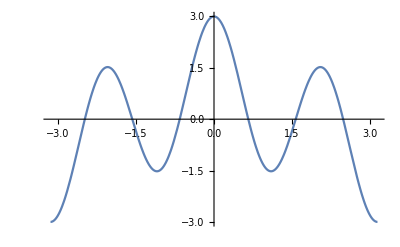

```mathematica
Plot[Cos[x]+2Cos[3x],{x,-Pi,Pi}]
```

```mathematica
ClearAll[circleSmoothietheRest]

circleSmoothietheRest[function_,variable_,numCir_]:=
Block[
{proto=FourierSeries[function,variable,numCir]//ComplexExpand,protoList2,protoList3,protoList4,cosCoeff,sinCoeff,
basicCosCoord,basicSinCoord,totalRadius,manipulatedCosCoord,manipulatedSinCoord,manipulatedCoord,lastYCoord,plotCoord,cirCenter,cirArguments,lastLinetoYaxis,combinedCir,lineSeries,range,fourierCoeff},
Print[proto];

protoList2=Drop[Apply[List,proto],1];
protoList3=Drop[protoList2,-numCir];
protoList4=Drop[protoList2,numCir];
cosCoeff=Insert[DeleteCases[protoList3/.Times->List//Flatten,_Cos],1,2];
sinCoeff=DeleteCases[protoList4/.Times->List//Flatten,_Sin];

fourierCoeff=Join[cosCoeff,sinCoeff];

totalRadius=Total[Abs@cosCoeff]+Total[Abs@sinCoeff];
	basicCosCoord=MapThread[Times,{cosCoeff,Cos[Range[numCir]*$time]}];
	basicSinCoord=MapThread[Times,{cosCoeff,Sin[Range[numCir]*$time]}];
	manipulatedCosCoord=Join[
		Take[
			Transpose[
			{(basicCosCoord-totalRadius-5)/.Cos->Sin,basicCosCoord}],1],
		Drop[Transpose[{basicCosCoord/.Cos->Sin,basicCosCoord}],1]];
	manipulatedSinCoord=Join[
		Take[
			Transpose[
			{(basicSinCoord-totalRadius-5)/.Sin->Cos,basicSinCoord}],1],
		Drop[Transpose[{basicSinCoord/.Sin->Cos,basicSinCoord}],1]];
	manipulatedCoord=Join[manipulatedCosCoord,manipulatedSinCoord];
	
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-totalRadius-5,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=Total[MapThread[Times,{cosCoeff,Cos[((Range[numCir])*(variable+$time))]}]]+Total[MapThread[Times,{sinCoeff,Sin[((Range[numCir])*(variable+$time))]}]];
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= Line[#1]&@(Append[manipulatedCoord,lastLinetoYaxis]);
	
	range=(2Pi)*totalRadius;

	Animate[
			Show[
				Graphics[{Sequence@@#1,#2},Axes->True],
				Plot[#3,{variable,0,30},PlotRange->Full],
				Plot[#4,{variable,0,30}],PlotRange->All
								],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord,function}]
	
	


]
```

```mathematica
circleSmoothietheRest[x^3+x,x,5]
```

-10 Sin[x]+2 π^2 Sin[x]+1/2 Sin[2 x]-π^2 Sin[2 x]+2/9 Sin[3 x]+2/3 π^2 Sin[3 x]-5/16 Sin[4 x]-1/2 π^2 Sin[4 x]+38/125 Sin[5 x]+2/5 π^2 Sin[5 x]

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Times,{{2,1,π^2,Sin[x],1/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],2/9,Sin[3],Sin[x]},{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],Cos[5 $time]}}]; dimensions are 14 and 5.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Times,{{2,1,π^2,Sin[x],1/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],2/9,Sin[3],Sin[x]},{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],Sin[5 $time]}}]; dimensions are 14 and 5.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {-202297/18000-4 π^2-4 Abs[Sin[x]]+MapThread[Times,{{2,1,π^2,Sin[x],1/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],2/9,Sin[3],Sin[x]},{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],Sin[5 $time]}}]-2 Sin[2]-Sin[3],MapThread[Times,{{2,1,π^2,Sin[x],1/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],2/9,Sin[3],Sin[x]},{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],Cos[5 $time]}}]} cannot be transposed.

Transpose::nmtx: The first two levels of {MapThread[Times,{{2,1,π^2,Sin[x],1/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],2/9,Sin[3],Sin[x]},{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],Sin[5 $time]}}],MapThread[Times,{{2,1,π^2,Sin[x],1/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],2/9,Sin[3],Sin[x]},{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],Cos[5 $time]}}]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::tperm: Permutation {-202297/18000-4 π^2-4 Abs[Cos[x]]-2 Cos[2]-Cos[3]+MapThread[Times,{{2,1,π^2,Cos[x],1/2,Cos[2],Cos[x],-1,π^2,Cos[2],Cos[x],2/9,Cos[3],Cos[x]},{Cos[$time],Cos[2 $time],Cos[3 $time],Cos[4 $time],Cos[5 $time]}}],MapThread[Times,{{2,1,π^2,Sin[x],1/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],2/9,Sin[3],Sin[x]},{Sin[$time],Sin[2 $time],Sin[3 $time],Sin[4 $time],Sin[5 $time]}}]} is longer than the dimensions {2} of the expression.

```mathematica
proto=FourierSeries[x^2+x,x,5]//ComplexExpand
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]-1/2 Sin[4 x]+2/5 Sin[5 x]

```mathematica
Drop[Apply[List,proto],1]
```

{-4 Cos[x],Cos[2 x],-4/9 Cos[3 x],1/4 Cos[4 x],-4/25 Cos[5 x],2 Sin[x],-Sin[2 x],2/3 Sin[3 x],-1/2 Sin[4 x],2/5 Sin[5 x]}

```mathematica
cos=MapThread[Times,{(Table[FourierCosCoefficient[x^2,x,p],{p,1,5}]),Cos[Range[5]*$time]}]
sin=MapThread[Times,{Table[FourierSinCoefficient[x^2+x,x,p],{p,1,5}],Sin[Range[5]*$time]}]
```

{-4 Cos[$time],Cos[2 $time],-4/9 Cos[3 $time],1/4 Cos[4 $time],-4/25 Cos[5 $time]}

{(2-8/π+2 π) Sin[$time],(-1-π) Sin[2 $time],2/27 (9-4/π+9 π) Sin[3 $time],1/2 (-1-π) Sin[4 $time],(2/5-8/(125 π)+(2 π)/5) Sin[5 $time]}

```mathematica
?DeleteCases
```

```mathematica
proto=FourierSeries[x^3-x,x,5]//ComplexExpand
proto2=Drop[Apply[List,proto],1]
proto3=Drop[proto2,-5]
proto4=Drop[proto2,5]
cosCoeff=Insert[DeleteCases[proto3/.Times->List//Flatten,_Cos],1,2]
sinCoeff=DeleteCases[proto4/.Times->List//Flatten,_Sin]
```

-14 Sin[x]+2 π^2 Sin[x]+5/2 Sin[2 x]-π^2 Sin[2 x]-10/9 Sin[3 x]+2/3 π^2 Sin[3 x]+11/16 Sin[4 x]-1/2 π^2 Sin[4 x]-62/125 Sin[5 x]+2/5 π^2 Sin[5 x]

{2 π^2 Sin[x],5/2 Sin[2 x],-π^2 Sin[2 x],-10/9 Sin[3 x],2/3 π^2 Sin[3 x],11/16 Sin[4 x],-1/2 π^2 Sin[4 x],-62/125 Sin[5 x],2/5 π^2 Sin[5 x]}

{2 π^2 Sin[x],5/2 Sin[2 x],-π^2 Sin[2 x],-10/9 Sin[3 x]}

{11/16 Sin[4 x],-1/2 π^2 Sin[4 x],-62/125 Sin[5 x],2/5 π^2 Sin[5 x]}

{2,1,π^2,Sin[x],5/2,Sin[2],Sin[x],-1,π^2,Sin[2],Sin[x],-10/9,Sin[3],Sin[x]}

{11/16,-1/2,π^2,-62/125,2/5,π^2}

```mathematica
proto=FourierSeries[x^2,x,5]//ComplexExpand
proto2=Drop[Apply[List,proto],1]
proto3=Drop[proto2,-5]
proto4=Drop[proto2,5]
cosCoeff=Insert[DeleteCases[proto3/.Times->List//Flatten,_Cos],1,2]
sinCoeff=DeleteCases[proto4/.Times->List//Flatten,_Sin]
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]

{-4 Cos[x],Cos[2 x],-4/9 Cos[3 x],1/4 Cos[4 x],-4/25 Cos[5 x]}

{}

{}

Insert::ins: Cannot insert at position {2} in {}

Insert[{},1,2]

{}

```mathematica
FourierSeries[x^3+x^2,x,5]//ComplexExpand
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]-12 Sin[x]+2 π^2 Sin[x]+3/2 Sin[2 x]-π^2 Sin[2 x]-4/9 Sin[3 x]+2/3 π^2 Sin[3 x]+3/16 Sin[4 x]-1/2 π^2 Sin[4 x]-12/125 Sin[5 x]+2/5 π^2 Sin[5 x]

```mathematica
Inse
```